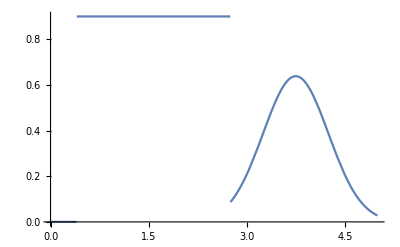

```mathematica
Clear[μ,σ]
μ:=3.750
σ:=0.5

G[x_]:=0.80Exp[-0.5(x-μ)^2/σ^2]/(σ*Sqrt[2*Pi])
FiltroVidrio[x_]:=If[x<0.4,0,If[x<2.75,0.90,G[x]]]
Plot[FiltroVidrio[x],{x,0,5}]
```

General::munfl: 1.17297×10^8 1.0522309093×10^-10429 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.17297×10^8 1.6122344244×10^-10085 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.17297×10^8 2.5739960384×10^-9763 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

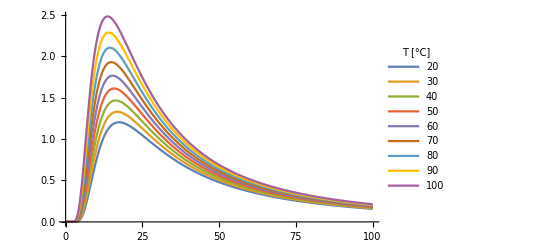

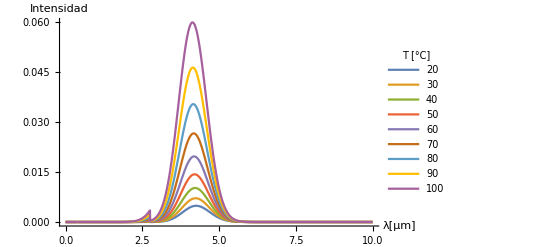

```mathematica
Clear[T]
ℏ:=6.582119624
k:=8.6173324
c:=299792458
s:=ℏ*c*2*Pi*10^{-5}/k
planck[x_,T_]:=10^{5}/(x^3*(Exp[s/(x*T)]-1))
f2[x_,T_]:=planck[x,T]*FiltroVidrio[x]
Plot[Evaluate@Table[planck[x,T+273.15],{T,{20,30,40,50,60,70,80,90,100}}],{x,0,100},PlotLegends->LineLegend[Table[b,{b,20,100,10}],LegendLabel->"T [°C]"]]
Plot[Evaluate@Table[f2[x,T+273.15],{T,{20,30,40,50,60,70,80,90,100}}],{x,0,10}, PlotRange->All, AxesLabel->{"λ[μm]","Intensidad"},PlotLegends->LineLegend[Table[b,{b,20,100,10}],LegendLabel->"T [°C]"]]
```

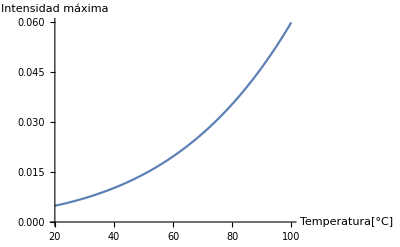

```mathematica
MaxF[T_]:=FindMaxValue[f2[x,T],{x,3}]
Plot[MaxF[T+273.15],{T,20,100}, AxesLabel->{"Temperatura[°C]","Intensidad máxima"}]
```